```mathematica
Ny=1024;
Nx=Round[Ny Sqrt[3]];
ymax=1;

width[y_]:=Sqrt[1-3(y/2)^2]
lon[x_,y_]:=Pi+2Pi (x-1/2)/width[y]
lat[y_]:=ArcSin[(9 y √(4-3 y^2)+12 √3 ArcSin[(√3 y)/2])/(9+4 √3 π)]

coords[j_,i_]:={Nlat-Round[Nlat*(Pi/2+lat[((Ny-N@j)/Ny)*2ymax-ymax])/(Pi)],
Round[Nlon*lon[N@i/Nx,((Ny-N@j)/Ny)*2ymax-ymax]/(2Pi)]}
get[{y_,x_}]:=If[1≤y≤Nlat&&1≤x≤Nlon,id[[y,x]],{1,1,1}]

Table[coords[j,i],{j,1,Ny},{i,1,Nx}];
%[[1,1]]
%%[[-1,-1]]
idM=Table[get[coords[j,i]],{j,1,Ny},{i,1,Nx}];
Image[idM]
```

{16,-1010}

{1024,3072}

-Graphics-

```mathematica
Export[Directory[]<>"/specialK.png",Image[idM]];
```

```mathematica
width[y_]:=Sqrt[1-3(y/2)^2]
```

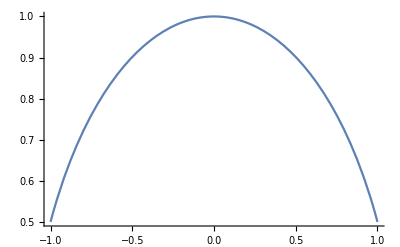

```mathematica
Plot[width[y],{y,-1,1}]
```

```mathematica
DSolve[L'[y]==a width[y]/(Pi Cos[L[y]]),L,y]
```

{{L→Function[{y},ArcSin[(3 a y √(4-3 y^2)+4 √3 a ArcSin[(√3 y)/2]+12 π C[1])/(12 π)]]}}

```mathematica
ArcSin[(3 a y √(4-3 y^2)+4 √3 a ArcSin[(√3 y)/2]+12 π C[1])/(12 π)]/.{C[1]->0,y->1}
```

ArcSin[(3 a+(4 a π)/(√3))/(12 π)]

```mathematica
Solve[%==Pi/2,a]
```

{{a→(36 π)/(9+4 √3 π)}}

```mathematica
ArcSin[(3 a y √(4-3 y^2)+4 √3 a ArcSin[(√3 y)/2]+12 π C[1])/(12 π)]/.{C[1]->0,a->(36 π)/(9+4 √3 π)}//Simplify
```

ArcSin[(9 y √(4-3 y^2)+12 √3 ArcSin[(√3 y)/2])/(9+4 √3 π)]

```mathematica
Sqrt[3]//N
```

1.73205